## 3. Domača naloga

### Naloga 1

Obravnavaj met žogice iz višine H v smeri vektorja v0 = {v0x, v0y}. Upoštevaj gravitacijski pospešek g =9.81m/s2. Pomagaj si z naslednjimi koraki:

Obravnavaj problem v ravnini, kjer je os x smer meta, os y pa predstavlja višino. Sestavi vektorsko (2D) funkcijo v[t_], ki za dan čas t izračuna vektor hitrosti pri metu. Izberi naslednje parametre:

```mathematica
v0={10,3};
GG=9.81;
H=10;
a = {0, -GG};
x0 ={0, H};
```

```mathematica
v[t_] := v0 + a*t
```

```mathematica
v[1]
```

{10,-6.81}

Vemo, da velja x(t)= x(0)+ ∫v(t)ⅆt 0 . Če veš, da je x0 = {0, H}, sestavi še vektorsko funkcijo X[t_], ki vrne položaj žogice ob času t.

```mathematica
X[t_] := x0 + v0*t + a*t^2/2
```

```mathematica
X[1]
```

{10,8.095}

Sestavi funkcijo SlikaTocke[t_], ki nariše žogo kot točko. Velikost točke naj bo 3% slike.

```mathematica
SlikaTocke[t_] := {PointSize[0.03],Point[X[t]]};
```

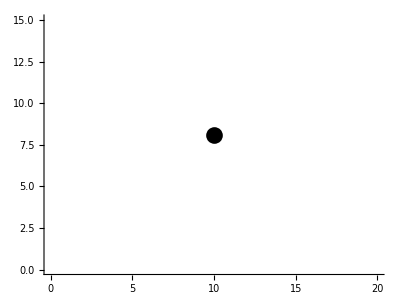

```mathematica
Graphics[SlikaTocke[1], Axes->True, PlotRange-> {{0,20}, {0, 15}}]
```

Sestavi funkcijo SlikaVektorja[t_], ki nariše vektor hitrosti iz točke. Uporabi graﬁčni objekt Arrow. Debelina črte naj bo 0,5% velikosti slike.

```mathematica
SlikaVektorja[t_] := {Thickness[0.005], Arrow[{X[t], X[t]+v[t]}]};
```

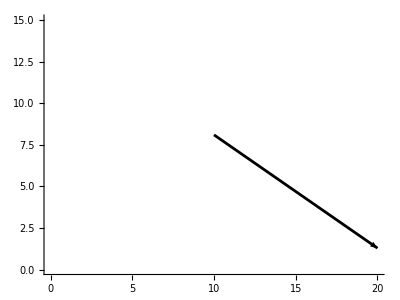

```mathematica
Graphics[SlikaVektorja[1], Axes->True, PlotRange-> {{0,20}, {0, 15}}]
```

Nariši sliko žoge in vektorja po eni sekundi. Na sliki naj se nariše koordinatni sistem, os x nastavi na interval [−1,25], os y pa na interval [−5,15]. Velikosti enot na obeh oseh naj bosta enaki (Namig: preveri delovanje naslednjih opcij v objektu Graphics: Axes, PlotRange in AspectRatio).

```mathematica
Slika[t_] := Graphics[{SlikaTocke[t], SlikaVektorja[t]}, Axes->True,
		PlotRange->{{-1, 25}, {-5, 15}}, AspectRatio->Automatic]
```

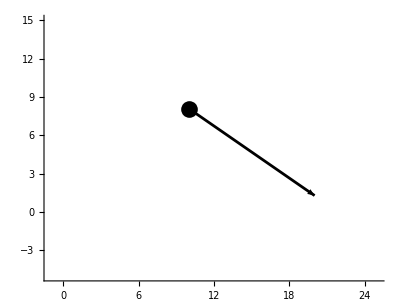

```mathematica
Slika[1]
```

S pomočjo funkcije Manipulate naredi animacijo leta žoge. Čas t premikaj o 0 do 5s.

```mathematica
Manipulate[Graphics[SlikaTocke[t], Axes->True, 
	PlotRange-> {{0,50}, {-50, 15}}], {t, 0, 5}]
```

Izračunaj čas padca žoge. Izračunaj še vrednost v smeri x, kjer žoga pade.

```mathematica
Enacba = ((H + v0 * t) - GG * t^2 / 2)[[2]]; 
CasPadca = Solve[Enacba == 0, t][[2]]
```

{t→1.76604}

Izračunaj čas doseganja največje višine leta ter maksimalno višino.

```mathematica
ClearAll[v]
```

```mathematica
v = (v0[[1]]^2 + v0[[2]]^2)^(1/2);
sinus = (v0[[2]]/v)//N;
casMax = (2 * v * sinus) / (2*GG)
MaxVisina = (v^2 * sinus^2)/(2*GG) + H
```

0.30581

10.4587

Uporabi izračuna iz zgornjih dveh točk tako, da bo območje izrisa čimbolj primerno (na osi x od -1 do malce več kot lokacija padca; na osi y pa naj bo od nekaj pod ničlo do malce več kot maksimalna višina leta; čas animacije naj bo od 0 do trenutka padca.

```mathematica
domet = v^2 *Sin[2*ArcSin[sinus]]/GG + H;
Manipulate[Graphics[{SlikaTocke[t]}, 
	Axes->True, PlotRange->{ {-1, domet+2},{-1, MaxVisina+1}}, 
		AspectRatio-> Automatic],{t, 0, 1.766035031964932}]
```

Kakšna je absolutna vrednost hitrosti v trenutku, ko žogica zadene tla?

```mathematica
ClearAll[v]
```

```mathematica
Cas = casMax+((2*MaxVisina)/(GG))^(1/2)
v[t_] := v0 + a*t;
absV = (v[Cas][[1]]^2 + v[Cas][[2]]^2)^(1/2)
```

1.76604

17.47

### Naloga 2

Ravnino podamo v obliki Ravnina[n_, v_], kjer je n normala na ravnino in je v točka na ravnini. Npr. ravnina, ki gre skozi točko (1,1,1) in je pravokotna na glavno diagonalo je r111 = Ravnina[{-1,-1,-1}, {1,1,1}].

```mathematica
r111 = Ravnina[{-1,-1,-1},{1,1,1}];
```

Sestavifunkcijo Slika[Ravnina[n_, v_]], kipripravi3Dgraﬁčniobjekt. Oglejsigraﬁčniobjekt Hyperplane.

```mathematica
Slika[Ravnina[n_, v_]] := Hyperplane[n, v]
```

Sestavi funkcijo Format[r_Ravnina], ki nariše ravnino. Pozor: če deﬁniramo funkcijo Format na objektih, se ti objekti “sami” izrišejo.

```mathematica
Format[r_Ravnina] := Graphics3D[Slika[r]]
```

```mathematica
Format[r111]
```

-Graphics3D-

Sestavi še priročni funkciji Normala[Ravnina[n_, v_]] in Tocka[Ravnina[n_, v_]], ki vrneta točko in normalo ravnine.

```mathematica
Normala[Ravnina[n_, v_]] := n;
Tocka[Ravnina[n_, v_]] := v;
```

Deﬁniraj koordinatne ravnine rx, ry, rz, ki gredo skozi točko 0 in so njihove normale enotski vektorji koordinatnih osi.

```mathematica
rx = Ravnina[{1, 0, 0}, {0, 0, 0}];
ry = Ravnina[{0, 1, 0}, {0, 0, 0}];
rz = Ravnina[{0, 0, 1}, {0, 0, 0}];
```

Sestavi funkcijo SlikaNormale[Ravnina[n_, v_]],ki vrne graﬁčni objekt slike normale. Uporabi graﬁčni objekt Arrow.

```mathematica
SlikaNormale[Ravnina[n_, v_]] := Arrow[{v, v + n}];
```

Nariši vse štiri ravnine rx, ry, rz, r111 na isti sliki skupaj z normalami.

```mathematica
ravnine = {r111, rx, ry, rz};
vseSlike[r_Ravnina] := {Slika[r],SlikaNormale[r]};
Graphics3D[Map[vseSlike, ravnine]]
```

-Graphics3D-

Sestavi funkcijo Enacba[Ravnina[n_, v_]], ki vrne enačbo ravnine.

```mathematica
ClearAll[v, a, b, c, Enacba]
```

```mathematica
Enacba[Ravnina[n_, v_]] := Module[{a, b, c, d},
	a = n[[1]];
	b = n[[2]];
	c = n[[3]]; 
	d = a*v[[1]] + b*v[[2]] + c*v[[3]];
	a*x + b*y + c*z == d]
```

```mathematica
Enacba[r111]
```

-x-y-z==-3

Sestavi funkcijo ResiSistem[sistem_List], ki za dan sistem treh enačb v spremenljivkah x, y in z vrne točko rešitve. Predpostavi, da je sistem takšen, da vrne samo eno rešitev.

```mathematica
SezEnacb = List[Enacba[r111], Enacba[rx], Enacba[ry]];
ResiSistem[sistem_List] := Solve[{sistem[[1]], sistem[[2]], sistem[[3]]}, 
	{x, y, z}]
```

```mathematica
ResiSistem[SezEnacb]
```

{{x→0,y→0,z→3}}

### Naloga 3

Izberi si neko 3D telo in ga nariši s pomočjo točk in poligonov. Enostavni primeri so kocke, kvadri. Bolj napredni so piramide, prizme, prerezane piramide...Bodite izvirni in narišite nekaj lepega. Narišite tudi normalo nad eno ploskvijo, ki gleda ven iz telesa iz težišča ploskve.

```mathematica
Graphics3D[Pyramid[{{0,0,0},{2,0,0},{2,2,0},{0,2,0},{1,1,2}}]]
```

-Graphics3D-